## Blunting neighborhoods + OAS constraint

```mathematica
everynbds = RegionPlot[{Abs[x]<=1, Abs[y]<=1},{x,-2,2},{y,-2,2}, 
BoundaryStyle->None, 
PlotStyle->{{Cyan, Opacity[0.5]},{Yellow, Opacity[0.5]}},
Frame->False,
Axes->True,
Ticks->False,
AxesLabel->{Style["epitope 1",24,Black],Style["epitope 2",24,Black]}];
```

```mathematica
anynbd = RegionPlot[Abs[x]<=1 && Abs[y]<=1, {x,-2,2},{y,-2,2}, 
BoundaryStyle->None, 
PlotStyle->{Green, Opacity[0.5]},
Frame->False,
Axes->True,
Ticks->False,
AxesLabel->{Style["epitope 1",24,Black],Style["epitope 2",24,Black]}];
```

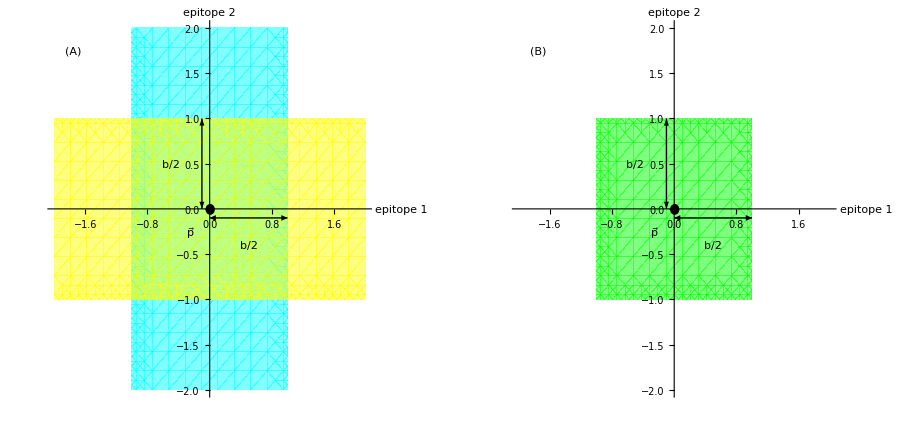

```mathematica
strainatorigin = Graphics[Disk[{0,0},.06]];
refpoint = Graphics[Style[Text[OverVector[p], {-.25,-.25}],FontSize->24]];
everyshow = Show[everynbds,strainatorigin,refpoint, 
Graphics[Style[Text["b/2",{-0.5,0.5}],FontSize->24]],Graphics[{Arrowheads[{-.03,.03}],Arrow[{{-0.1,1},{-0.1,0}}]}],
Graphics[Style[Text["b/2",{0.5,-0.4}],FontSize->24]],Graphics[{Arrowheads[{-.03,.03}],Arrow[{{0,-0.1},{1,-0.1}}]}],
Graphics[Style[Text["(A)",{-1.75,1.75}],FontSize->24]],ImageSize->450];
anyshow = Show[anynbd,strainatorigin,refpoint,
Graphics[Style[Text["b/2",{0.5,-0.4}],FontSize->24]],Graphics[{Arrowheads[{-.03,.03}],Arrow[{{-0.1,1},{-0.1,0}}]}],
Graphics[Style[Text["b/2",{-0.5,.5}],FontSize->24]],Graphics[{Arrowheads[{-.03,.03}],Arrow[{{0,-0.1},{1,-0.1}}]}],
Graphics[Style[Text["(B)",{-1.75,1.75}],FontSize->24]],ImageSize->450];
roworg = GraphicsRow[{everyshow, anyshow}];
rowtoexport=Show[roworg,ImageSize->900]
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

```mathematica
Export["../figures/blunting_nbds.pdf",rowtoexport]
```

../figures/blunting_nbds.pdf